```mathematica
Eff=Import[NotebookDirectory[]<>"../calc/efficencies.txt","Table"];
Eff//MatrixForm
EffErr=Import[NotebookDirectory[]<>"../calc/efficencies_error.txt","Table"];
EffErr//MatrixForm
```

(0.391474 | 0.0000106 | 0.00440579 | 0.00001015
0.00015991 | 0.890762 | 0.00358522 | 0.
0.00179101 | 0.00425933 | 0.747406 | 0.00235382
0. | 0. | 0.00186836 | 0.966965)

(0.00159362 | 0.0000106 | 0.00023532 | 0.00001015
0.00004129 | 0.00101537 | 0.00021236 | 0.
0.00013806 | 0.00021198 | 0.00154379 | 0.00015435
0. | 0. | 0.00015343 | 0.00056929)

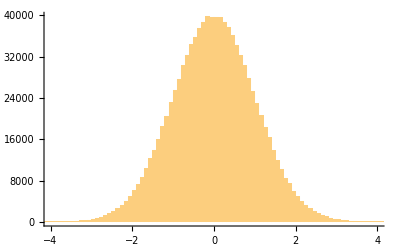

```mathematica
rns=Table[Table[RandomVariate[NormalDistribution[]],{j,1,4},{k,1,4}],{i,1,1000000}];
Histogram[rns[[All,1,1]],100,PlotRange->{{-4,4},All}]
```

```mathematica
NoisyInvEff=Inverse[Eff+EffErr*#]&/@rns;
```

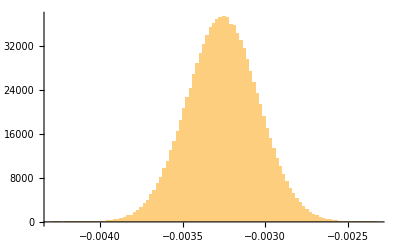

```mathematica
Histogram[NoisyInvEff[[All,3,4]],100,PlotRange->{All,All}]
```

```mathematica
NoisyInvEffSort=Table[NoisyInvEff[[All,i,j]],{i,1,4},{j,1,4}];
Inverse[Eff]
A=Mean[#]&/@#&/@NoisyInvEffSort;
A//MatrixForm
EffErr//MatrixForm
sA=StandardDeviation[#]&/@#&/@NoisyInvEffSort;
sA//MatrixForm
```

{{2.55452,0.0000416064,-0.0150585,9.84186×10^-6},{-0.00043396,1.12266,-0.00538275,0.0000131074},{-0.00611897,-0.00639798,1.33804,-0.00325703},{0.000011823,0.0000123621,-0.00258534,1.03417}}

(2.55457 | 0.0000416099 | -0.0150584 | 9.80682×10^-6
-0.000433789 | 1.12266 | -0.00538238 | 0.0000131058
-0.00612003 | -0.00639825 | 1.33804 | -0.00325685
0.0000118254 | 0.0000123631 | -0.00258546 | 1.03417)

(0.00159362 | 0.0000106 | 0.00023532 | 0.00001015
0.00004129 | 0.00101537 | 0.00021236 | 0.
0.00013806 | 0.00021198 | 0.00154379 | 0.00015435
0. | 0. | 0.00015343 | 0.00056929)

(0.0103983 | 0.0000308733 | 0.000807708 | 0.0000269752
0.000118288 | 0.0012801 | 0.000319369 | 1.16042×10^-6
0.000472407 | 0.000318912 | 0.00276422 | 0.000213848
1.33411×10^-6 | 1.1896×10^-6 | 0.00021257 | 0.000609221)

```mathematica
Round[Eff.A,10^-4]//MatrixForm
AccountingForm[MatrixForm[sA],2]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(0.01 | 0.000031 | 0.00081 | 0.000027
0.00012 | 0.0013 | 0.00032 | 0.0000012
0.00047 | 0.00032 | 0.0028 | 0.00021
0.0000013 | 0.0000012 | 0.00021 | 0.00061)

```mathematica
Export[NotebookDirectory[]<>"../calc/invEfficencies_Math.txt",A,"Table"];
sAexp=SetPrecision[sA,2];
Export[NotebookDirectory[]<>"../calc/invEfficencies_error_Math.txt",ToString[AccountingForm[#,2]]&/@#&/@sA,"Table"];
```

```mathematica
Quiet[100EffErr/Eff]//MatrixForm
Abs[100sA/Inverse[Eff]]//MatrixForm
```

(0.407082 | 100. | 5.34115 | 100.
25.8208 | 0.113989 | 5.92321 | Indeterminate
7.7085 | 4.97684 | 0.206553 | 6.55743
Indeterminate | Indeterminate | 8.21201 | 0.0588739)

(0.407055 | 74.2032 | 5.36378 | 274.086
27.2578 | 0.114023 | 5.93319 | 8.85314
7.72037 | 4.98458 | 0.206588 | 6.56573
11.284 | 9.62299 | 8.22212 | 0.0589092)

```mathematica
Inverse[Eff].EffErr.Inverse[Eff]//MatrixForm
```

(0.0103904 | 0.0000233353 | 0.000711781 | 0.0000225746
0.000112847 | 0.00127698 | 0.000300942 | -1.5898×10^-6
0.000433573 | 0.000297877 | 0.00275485 | 0.000204889
-1.80169×10^-6 | -1.58345×10^-6 | 0.000205463 | 0.000607943)